```mathematica
(*Example 1 map from Article,see article_example01.m (Matlab) for numerical calculation*)
A1={{1,1,1},{1,2,0},{1,0,2}};
A2={{3,-1,0},{-1,0,-1},{0,-1,1}};
A3={{1,0,0},{0,1,0},{0,0,1}};
b=Transpose[{{1,1,1},{1,0,-1},{0,0,0}}];
{b1,b2,b3}=Transpose[b];
A={A1,A2,A3};
A1//MatrixForm
A2//MatrixForm
A3//MatrixForm
b//MatrixForm
(* defining y=f(x) *)
y1={x1, x2, x3}.A1.{x1,x2,x3}+2*b1.{x1,x2,x3};
y2={x1, x2, x3}.A2.{x1,x2,x3}+2*b2.{x1,x2,x3};
y3={x1, x2, x3}.A3.{x1,x2,x3}+2*b3.{x1,x2,x3};
```

(1 | 1 | 1
1 | 2 | 0
1 | 0 | 2)

(3 | -1 | 0
-1 | 0 | -1
0 | -1 | 1)

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

(1 | 1 | 0
1 | 0 | 0
1 | -1 | 0)

```mathematica
(* Taking the solution x(Y), replacing root with List, taking the polynomial out *)
S = Solve[y1==Y1 && y2 ==Y2 && y3 == Y3 , {x1, x2, x3}] 
Poly:=((List @@ (x1/.S[[1]]))[[1]])
```

{{x1→Root[32 Y1^2+8 Y1^3+5 Y1^4+64 Y1 Y2+32 Y1^2 Y2+24+(2688-736 Y1-248 Y1^2-2688 Y2+256 Y1 Y2+256 Y2^2+6112 Y3+480 Y1 Y3-1280 Y2 Y3+608 Y3^2) #1^3+(4512-808 Y1+94 Y1^2-2400 Y2+128 Y1 Y2+64 Y2^2+5624 Y3-648 Y1 Y3-448 Y2 Y3+1064 Y3^2) #1^4+(4368-824 Y1-960 Y2+2848 Y3) #1^5+(2616+44 Y1-96 Y2-144 Y3) #1^6+696 #1^7+261 #1^8&,1],x2→1/1,x3→(349+1377558 Y3^2 1^7)/(13167360+9210240 Y1+68+108160 Y3^5)},6,{1}}
 |  |  |  |

```mathematica
(* Care about the boundary -> taking discriminant *)
Quq=Discriminant[Poly[z], z]
```

18807032043899191296 (13134378933714217402368 Y1^2+74831326227576855724032 Y1^3+193333566202802360082432 Y1^4+301843711422119961538560 Y1^5+321531252513768427864320 Y1^6+251682405599505893596416 Y1^7+153541756463195685994560 Y1^8+6118+1193398265704152268800 Y2 Y3^26+167410624396857753600 Y1 Y2 Y3^26+49113483008099328000 Y2^2 Y3^26-212904361939516416000 Y3^27-26108699177014272000 Y1 Y3^27-16256813966714880000 Y2 Y3^27+2473227593740800000 Y3^28)
 |  |  |  |

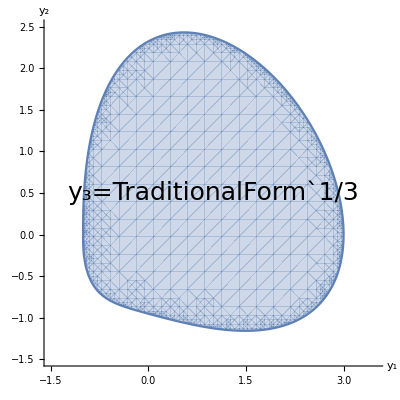

```mathematica
(* Plotting first section y3=1/3. We are lucky and can just take poly2 ≤ 0 *)
Y3sec =1/3;
Qplot = Quq/.{Y3 -> Y3sec};
poly2 = Factor[Qplot][[4]];
RegionPlot[poly2≤0,{Y1,-1.5,3.5},{Y2,-1.5,2.5},Axes->True,Frame->None,AxesStyle->Directive[Black,40],TicksStyle->Directive[Black, 20],AxesLabel->{Style["y_1",FontSize->22],Style["y_2",FontSize->22]}, MaxRecursion->4,Epilog->{Text[Style[StringForm["y_3=`1`",Y3sec],25],Scaled[{0.5,0.5}]]},BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->20}]
```

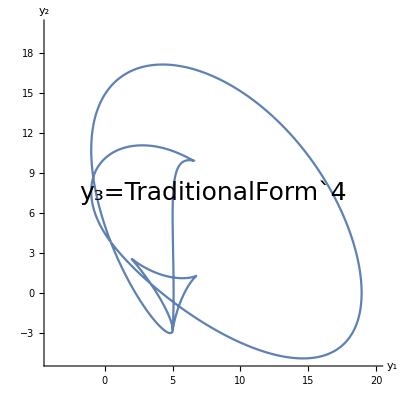

```mathematica
(* Plotting the y3=4 section. Less lucky, RegionPlot doesn't work, so we use polar plot manually (furthest point) *)
Y3sec =4;
Qplot = Quq/.{Y3 -> Y3sec};
poly2 = Factor[Qplot][[4]];
plot=ContourPlot[poly2==0,{Y1,-4,20},{Y2,-5,20},Axes->True,Frame->None,AxesStyle->Directive[Black,40],TicksStyle->Directive[Black, 20],AxesLabel->{Style["y_1",FontSize->22],Style["y_2",FontSize->22]}, MaxRecursion->4,Epilog->{Text[Style[StringForm["y_3=`1`",Y3sec],25],Scaled[{0.5,0.5}]]},BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->20}]
```

```mathematica
(* points from the plot *)
points=Cases[Normal@plot,Line[pts_,___]:>pts,Infinity];
list=Flatten[points,1];
```

```mathematica
(* shifting the points so that polar coordinates from the point inside map it properly (assessed visually) *)
xdiff=4;
ydiff=0;
pts=list+ConstantArray[{-xdiff,-ydiff},Length[list]];
```

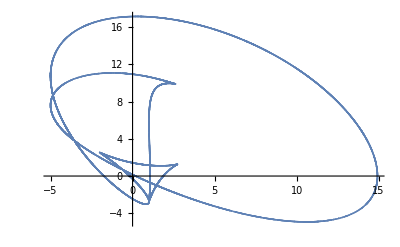

```mathematica
ListPlot[pts]
```

```mathematica
(* going to polar coordinates *)
r=Norm/@pts;
phi=(ArcTan@@#1)&/@pts;
d=0.01; (* threshold angle *)
(* function: max r s.t. exist a point on a ray alpha in pts *)
rad[alpha_]:=Max[MapThread[If[#1≤d,r[[#2]],0]&,{Abs[phi-alpha],Range[1,Length[phi]]}]];
```

```mathematica
(* ranges of phis, and corresponding Rs *)
phis1=Range[-Pi,Pi,0.01];
rs1=rad/@phis1;
```

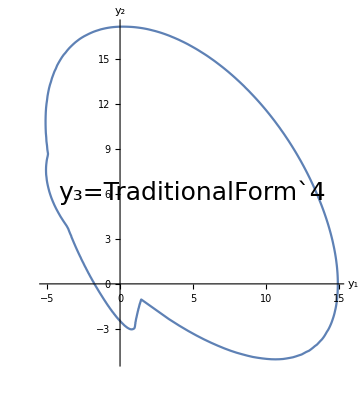

```mathematica
(* plotting in polar coordinates *)
ListPolarPlot[Transpose[{phis1,rs1}],Joined->True,Axes->True,Frame->None,AxesStyle->Directive[Black,40],TicksStyle->Directive[Black, 20],AxesLabel->{Style["y_1",FontSize->22],Style["y_2",FontSize->22]}, Epilog->{Text[Style[StringForm["y_3=`1`",Y3sec],25],Scaled[{0.5,0.5}]]},BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->20}]
```

Nearest::dmtch: The dimension of {-3.14159, -3.13159, -3.12159, -3.11159, -3.10159, -3.09159, -3.08159, -3.07159, -3.06159, -3.05159, -3.04159, -3.03159, « 28 », -2.74159, -2.73159, -2.72159, -2.71159, -2.70159, -2.69159, -2.68159, -2.67159, -2.66159, -2.65159, « 579 »} and ArcTan[-4 + x, y] does not match.

Part::pkspec1: The expression ArcTan[-4 + x, y] cannot be used as a part specification.

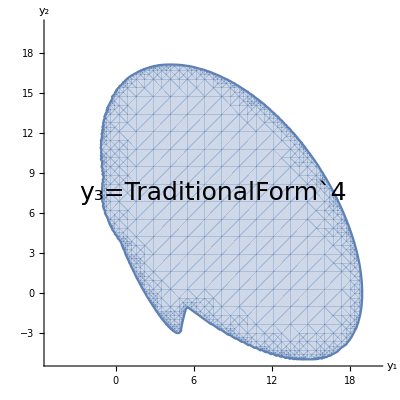

```mathematica
(* plotting the area inside *)
(* closest phi angle *)
nf=Nearest[phis1->Automatic];
(* is this point inside the shape? *)
IsInside[x_,y_]:=Norm[{x-xdiff,y-ydiff}]≤rs1[[nf[ArcTan[x-xdiff,y-ydiff]][[1]]]];
(* plotting the shape *)
RegionPlot[IsInside[x,y],{x,-5,20},{y,-5,20},Axes->True,Frame->None,AxesStyle->Directive[Black,40],TicksStyle->Directive[Black, 20],AxesLabel->{Style["y_1",FontSize->22],Style["y_2",FontSize->22]}, MaxRecursion->4,Epilog->{Text[Style[StringForm["y_3=`1`",Y3sec],25],Scaled[{0.5,0.5}]]},BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->20}]
```